## Data Input

```mathematica
Ey0data={     {41, 0.282, -28.64},{51, 0.419, -41.1}, {61,0.559, -47.3} , {71, 0.696, -54}, {33, 0.510, -23.2}, {43, 0.806, -47.07}, {53, 0.922, -46.78}, {35, 0.808, -47.27}, {65, 0.999, -152.1}, {75, 0.999, -128.5}, {37, 0.921, -70}, {47, 0.999, -53.5}                  }
```

{{41,0.282,-28.64},{51,0.419,-41.1},{61,0.559,-47.3},{71,0.696,-54},{33,0.51,-23.2},{43,0.806,-47.07},{53,0.922,-46.78},{35,0.808,-47.27},{65,0.999,-152.1},{75,0.999,-128.5},{37,0.921,-70},{47,0.999,-53.5}}

```mathematica
Ey0dataPlot1={     {0.282, -28.64},{0.419, -41.1}, {0.559, -47.3} , {0.696, -54}, {0.510, -23.2}, {0.806, -47.07}, {0.922, -46.78}, {0.808, -47.27}, {0.999, -152.1}, {0.999, -128.5}, {0.921, -70}, {0.999, -53.5}                  }
```

{{0.282,-28.64},{0.419,-41.1},{0.559,-47.3},{0.696,-54},{0.51,-23.2},{0.806,-47.07},{0.922,-46.78},{0.808,-47.27},{0.999,-152.1},{0.999,-128.5},{0.921,-70},{0.999,-53.5}}

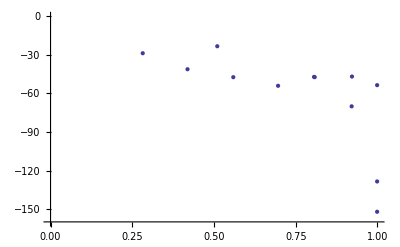

```mathematica
ListPlot[Ey0dataPlot1,PlotRange->{{0.0,1.0},{-160,0}},AxesStyle->Thick,AxesOrigin->{0,-160}]
```

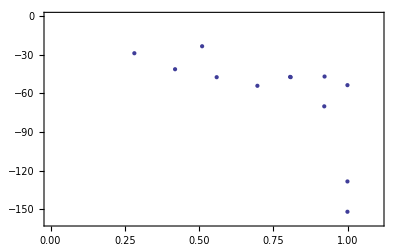

```mathematica
ListPlot[Ey0dataPlot1,PlotRange->{{0.0,1.1},{-160,0}},AxesOrigin->{0,-160},Frame-> True,FrameStyle-> Thick]
```

```mathematica
(*PlotRange->{{-0.0,1.02},{-160,0}},AxesOrigin->{0,-160},Frame-> {{True,True},{True,True}},FrameLabel->{{"Binding Energy  ( kcal/mol )",Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Subscript[y, 0],}},LabelStyle-> {Italic,Bold},FrameStyle-> {{Thick,None},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio*)
```

Syntax::tsntxi: "figureformat = PlotRange → {{-0.0, 1.02}, {-160, 0}}, AxesOrigin → {0, -160}, Frame → {{True, True}, {True, True}}, « 1 », LabelStyle → {« 1 »}, FrameStyle → {{Thick, None}, {Thick, Thick}}, AspectRatio → 1/GoldenRatio" is incomplete; more input is needed.

Syntax::sntxi: Incomplete expression; more input is needed.

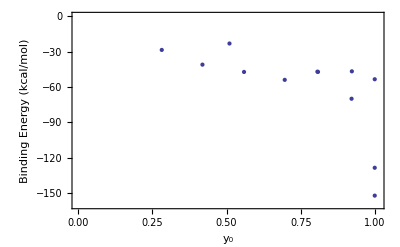

```mathematica
(*dataall=ListPlot[Ey0dataPlot1,PlotRange->{{-0.0,1.01},{-160,0}},AxesOrigin->{0,-160},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Style[Subscript[y, 0],17],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio]*)
dataall=ListPlot[Ey0dataPlot1,PlotRange->{{-0.0,1.01},{-160,0}},AxesOrigin->{0,-160},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Italic,17]},{Style[Subscript[y, 0],17],}},AspectRatio-> 1/GoldenRatio]
```

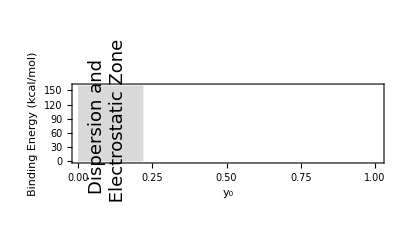

```mathematica
(*VdW=Graphics[{ {LightGray,Rectangle[{0,0},{0.22,160}]},{Black,Text[Style["Dispersion and \n Electrostatic Zone",Medium,Bold,Italic,18],{0.1,80},{0,0},{0,1}]} },PlotRange->{{0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Style[Subscript[y, 0],17],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio]*)
VdW=Graphics[{ {LightGray,Rectangle[{0,0},{0.22,160}]},{Black,Text[Style["Dispersion and \n Electrostatic Zone",Medium,Italic,18],{0.1,80},{0,0},{0,1}]} },PlotRange->{{0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Italic,17]},{Style[Subscript[y, 0],17],}},AspectRatio-> 1/GoldenRatio]
```

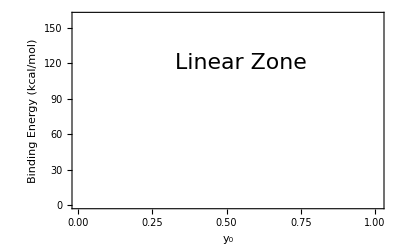

```mathematica
(*LZ=Graphics[{ {Black,Text[Style["Linear Zone",Medium,Bold,Italic,22],{0.55,120},{0,0},{1,0}]} },PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Style[Subscript[y, 0],17],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio]*)
LZ=Graphics[{ {Black,Text[Style["Linear Zone",Medium,Italic,22],{0.55,120},{0,0},{1,0}]} },PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Italic,17]},{Style[Subscript[y, 0],17],}} ,AspectRatio-> 1/GoldenRatio]
```

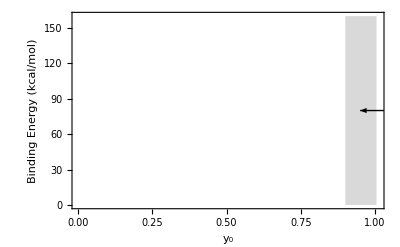

```mathematica
(*MDZ=Graphics[ {{LightGray,Rectangle[{0.9,160},{1.005,0}]}, {Black,Arrow[{{1.05,80},{0.95,80}}]} },PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Style[Subscript[y, 0],17],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio]*)
MDZ=Graphics[ {{LightGray,Rectangle[{0.9,160},{1.005,0}]}, {Black,Arrow[{{1.05,80},{0.95,80}}]} },PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Italic,17]},{Style[Subscript[y, 0],17],}},AspectRatio-> 1/GoldenRatio]
```

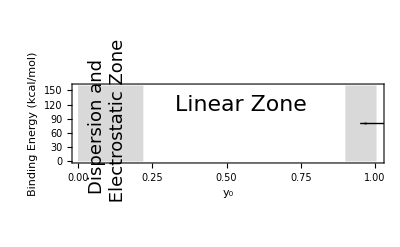

```mathematica
Show[VdW,LZ,MDZ,dataall]
```

```mathematica
Ey0datarow1= {{0.282, 28.64},{0.419, 41.1}, {0.559, 47.3} , {0.696, 54}}
Ey0datarow3={ {0.510, 23.2}, {0.806, 47.07}, {0.922, 46.78} }
Ey0datarow5={ {0.808, 47.27}, {0.999, 152.1}, {0.999, 128.5} }
Ey0datarow7={ {0.921, 70}, {0.999, 53.5} }
```

{{0.282,28.64},{0.419,41.1},{0.559,47.3},{0.696,54}}

{{0.51,23.2},{0.806,47.07},{0.922,46.78}}

{{0.808,47.27},{0.999,152.1},{0.999,128.5}}

{{0.921,70},{0.999,53.5}}

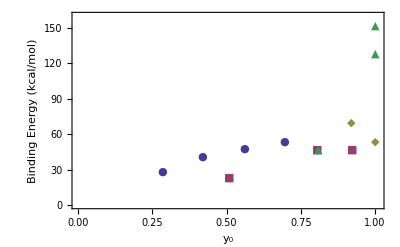

```mathematica
(*datarow=ListPlot[{Ey0datarow1,Ey0datarow3,Ey0datarow7,Ey0datarow5},PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Style[Subscript[y, 0],17],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio,PlotMarkers-> {Automatic,Medium}]*)
datarow=ListPlot[{Ey0datarow1,Ey0datarow3,Ey0datarow7,Ey0datarow5},PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,0},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Italic,17]},{Style[Subscript[y, 0],17],}} ,AspectRatio-> 1/GoldenRatio,PlotMarkers-> {Automatic,Medium}]
```

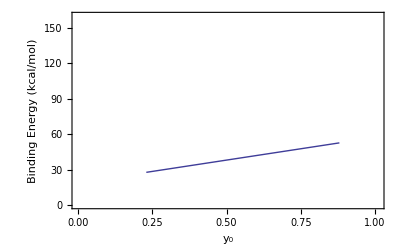

```mathematica
(*fitline=Plot[38.4x+18.8,{x,0.23,0.88},PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,-160},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Style[Subscript[y, 0],17],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio]*)
fitline=Plot[38.4x+18.8,{x,0.23,0.88},PlotRange->{{-0.0,1.01},{0,160}},AxesOrigin->{0,-160},Frame-> {{True,True},{True,True}},FrameLabel->{{Style["Binding Energy (kcal/mol)",16],Style["Multi-Dimension Zone",Medium,Italic,17]},{Style[Subscript[y, 0],17],}},AspectRatio-> 1/GoldenRatio]
```

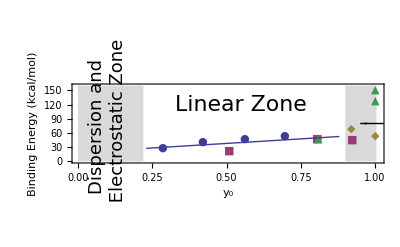

```mathematica
Show[VdW,LZ,MDZ,datarow,fitline]
```

```mathematica
M06largedata={{0.282,-22.36},{0.419,-37.97},{0.51,-25.55},{0.806,-58.49},{0.808,-61.00}}
```

{{0.282,-22.36},{0.419,-37.97},{0.51,-25.55},{0.806,-58.49},{0.808,-61.}}

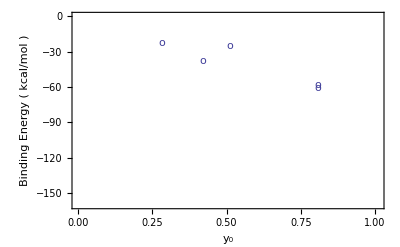

```mathematica
datalarge=ListPlot[M06largedata,PlotRange->{{-0.0,1.01},{-160,0}},AxesOrigin->{0,-160},Frame-> {{True,True},{True,True}},FrameLabel->{{"Binding Energy  ( kcal/mol )",Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Subscript[y, 0],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio,PlotMarkers-> {"o",Medium}]
```

```mathematica
M06small={{0.282,-23.51},{0.419,-39.12},{0.559,-46.55},{0.696,-54.34},{0.51,-24.76},{0.808,-57.66}}
```

{{0.282,-23.51},{0.419,-39.12},{0.559,-46.55},{0.696,-54.34},{0.51,-24.76},{0.808,-57.66}}

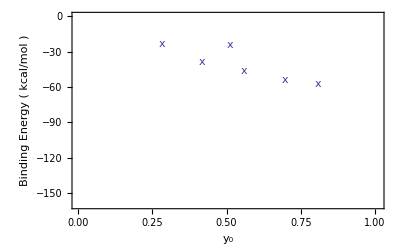

```mathematica
datasmall=ListPlot[M06small,PlotRange->{{-0.0,1.01},{-160,0}},AxesOrigin->{0,-160},Frame-> {{True,True},{True,True}},FrameLabel->{{"Binding Energy  ( kcal/mol )",Style["Multi-Dimension Zone",Medium,Bold,Italic,17]},{Subscript[y, 0],}},LabelStyle-> {Bold},FrameStyle-> {{Thick,Thick},{Thick,Thick}} ,AspectRatio-> 1/GoldenRatio,PlotMarkers-> {"x",Medium}]
```

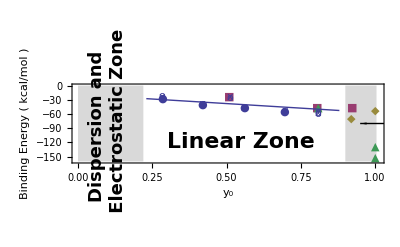

```mathematica
Show[VdW,LZ,MDZ,datarow,fitline,datalarge,datasmall]
```

## Draft

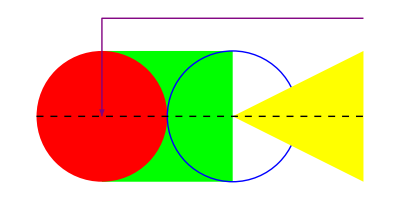

```mathematica
Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]
```

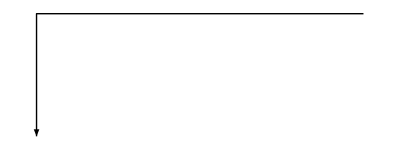

```mathematica
Graphics[{Arrow[{{4,3/2},{0,3/2},{0,0}}]}]
```

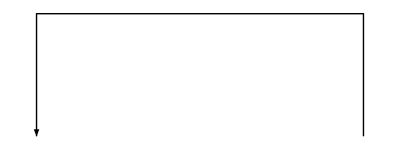

```mathematica
Graphics[{Arrow[{{4,0},{4,3/2},{0,3/2},{0,0}}]}]
```

```mathematica
Import["C:\Users\dodo\Desktop\novel_path_nucleation_v1_0613Pm08.xls"]
```

Import::nffil: File not found during Import.

$Failed